```mathematica
normalizedBgCorrectedGFP = N[
normalizeByInitialColValue[
subtractOneColFromAllColAndPositify[gfpData,50 ]
]
];
```

```mathematica
normalizedBgCorrectedRFP = N[
normalizeByInitialColValue[
subtractOneColFromAllColAndPositify[gfpData,39 ]
]
];
```

```mathematica
generateCombinedPlotOfColumn[dataMat01_,dataMat02_, colNum_]:=(
Block[{combinedPlot,timeArray01,timeArray02, array01AtColNum,array02AtColNum, plot01, plot02, plotID},
timeArray01 = getTimeArray[dataMat01];
timeArray02 = getTimeArray[dataMat02];

plotID = dataMat01[[1, colNum]];
If[
plotID == "H12",
plotID = ""
];
array01AtColNum =  ToExpression[ Delete[dataMat01[[All,colNum]], 1]];
array02AtColNum =  ToExpression[ Delete[dataMat02[[All,colNum]], 1]];

plot01 = generateSinglePlotWithColor[timeArray01, array01AtColNum, plotID, plotRangeInput, gfpPlotColor];
plot02 = generateSinglePlotWithColor[timeArray02, array02AtColNum, plotID, plotRangeInput, rfpPlotColor];
combinedPlot = Show[{plot01,plot02}];

Return[combinedPlot];
];
);
```

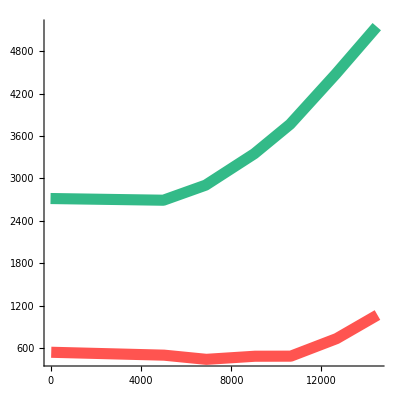

```mathematica
generateCombinedPlotOfColumn[gfpData, rfpData, 6]
```

```mathematica
makePdf[normalizedBgCorrectedRFP, 8, 12]
```

```mathematica
(* -----------------------------------------------;
	In: imported data, no. of rows, no.of columns;
	Out: Void. Creates a pdf in my documents folder.
*)
makePdfGfpRfp[dataMat01Global_,dataMat02Global_,numberOfRowsGlobal_,numberOfColumnsGlobal_ ]:=(
Block[{plotMatrix, label},
f[dataMat01_,dataMat02_, numberOfRows_, numberOfColumns_]:=(
Block[{graphHolder,k},
k=4;
graphHolder = Table[
k++;generateCombinedPlotOfColumn[dataMat01,dataMat02,k], 
{i,1,numberOfRows},
{j,1,numberOfColumns}
];
Return[graphHolder];
]
);

plotMatrix = f[dataMat01Global, dataMat02Global,numberOfRowsGlobal, numberOfColumnsGlobal];
label = Text[Style[plotInfo,6, RGBColor[40/255,40/255,40/255]]];
Export[
"myPlot.pdf",
GraphicsGrid[
plotMatrix,
Epilog->Inset[label, {4480,-2900}]
]
]
]
);
```

```mathematica
makePdfGfpRfp[gfpData, rfpData, 8, 12]
```

myPlot.pdf

```mathematica
SystemOpen["myPlot.pdf"]
```